Linear Multivariate Regression

{-0.522609,0.0102211,-0.020873,-0.00639456,-0.0520219,0.610259}

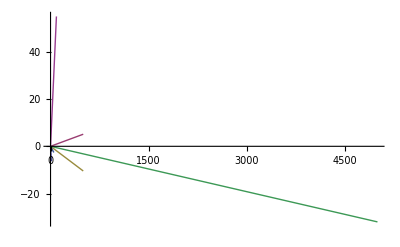

```mathematica
Multivariate Linear Regression

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
X = autoMPGDataSet[[1;;Length[autoMPGDataSet],2;;7]];
Y=autoMPGDataSet[[1;; Length[autoMPGDataSet],1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y)

predictedMPG = Table[β  . X[[i,All]],{i,Length[X]}];

predictedSeperator1 = Table[β[[1]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[2]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[4]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[5]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[6]]*featureValue,{featureValue,90}];
ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]
```

### Multivariate Linear Regression w/ Threshold (w0)

Inverse::luc: Result for Inverse of badly conditioned matrix {{392., 2145., 76209.5, 40952., 1.16721×10^6, 6092.2, 29784.}, {2145., 12875., 483375., 245728., 6.89538×10^6, 32407.5, 162127.}, {76209.5, 483375., 1.90976×10^7, 9.37465×10^6, 2.59345×10^8, 1.12301×10^6, 5.73462×10^6}, {40952., « 5 », « 12 »}, {1.16721×10^6, 6.89538×10^6, 2.59345×10^8, 1.3299×10^8, 3.75758×10^9, 1.77581×10^7, 8.83062×10^7}, {6092.2, 32407.5, 1.12301×10^6, 607832., 1.77581×10^7, 97656.9, 464036.}, {29784., 162127., 5.73462×10^6, 3.08843×10^6, 8.83062×10^7, 464036., 2.26828×10^6}} may contain significant numerical errors.

{-14.5353,-0.329859,0.00767843,-0.000391356,-0.00679462,0.0852732,0.753367}

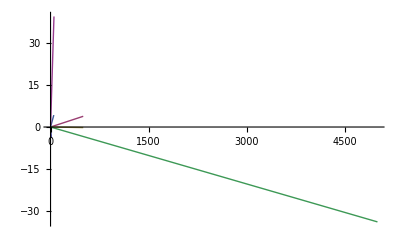

```mathematica
autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
X = autoMPGDataSet[[1;;Length[autoMPGDataSet],2;;7]];
unaryRow=Table[1,{Length[autoMPGDataSet]}];
X = Insert[X//Transpose,unaryRow,1]//Transpose;

Y=autoMPGDataSet[[1;; Length[autoMPGDataSet],1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y)

predictedMPG = Table[β  . X[[i,All]],{i,Length[X]}];

predictedSeperator1 = Table[β[[2]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[4]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[5]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[6]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[7]]*featureValue,{featureValue,90}];
ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]
```

### Quadratic regression

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];

(*
X = autoMPGDataSet[[1;;Length[autoMPGDataSet],2;;7]];
combinations = Table[Multisets[{2,3,4,5,6,7},k],{k,2,2,1}];
tail = Table[Product [autoMPGDataSet[[instance,combinations[[1,i,j]]]], {j,1,Length[combinations[[1,1]]]}],
{instance,1, Length[autoMPGDataSet]},
{i,1,Length[combinations[[1]]]}] ;

X = Insert[X//Transpose,unaryRow,1]//Transpose;
X = Join [X , tail ,2];*)

(*unaryRow=Table[1,{Length[autoMPGDataSet]}];
newX=Insert[newX//Transpose,unaryRow,1]//Transpose;*)

listCombo = {};
Manipulate[
For[i=1,i≤degree,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose;

Y=autoMPGDataSet[[1;; Length[autoMPGDataSet],1]];

β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);

vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor],
{degree,1,3,1}]
```